SEMIARCO 3A4 QUINTICO

-Graphics3D-

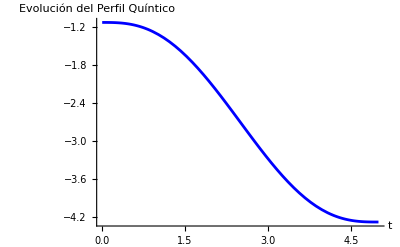

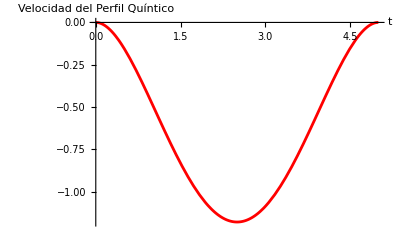

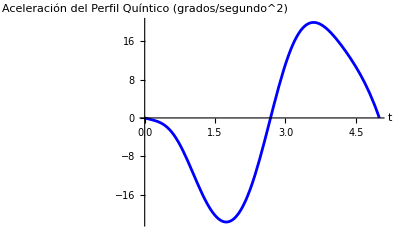

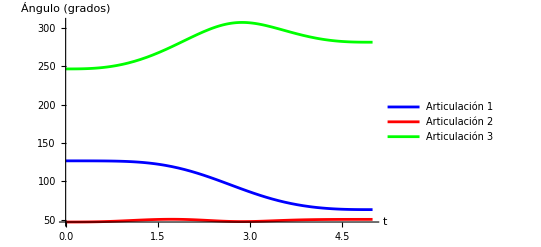

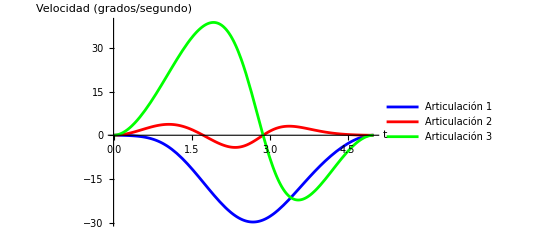

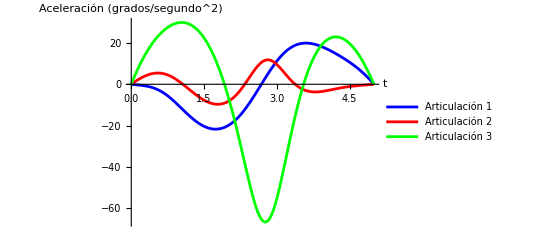

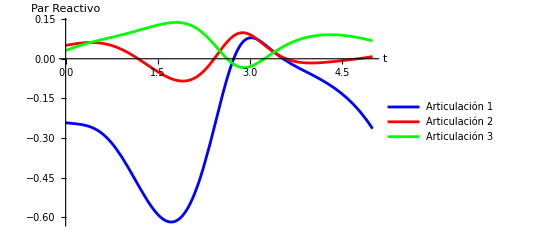

```mathematica
SEMIARCO 3A4 QUINTICO
(*Suposición:los eslabones están hecho de MDF*)(*densidad MDF=500[kg/m^3]*)(*densidad ABS=1040[kg/m^3]*)(*Se considerará un peso 10 veces menor,pues los eslaboness serán diseñados para tener el material minimo en manufactura aditiva*)ρ=1040/10;
g=-9.81;(*Aceleración gravitatoria*)

(*Datos del eslabón 1 o Cilindro*)
d1=15;(*Valor de d1/Altura del cilindro*)
RadCil=2.5;(*Radio Cilindro*)
m[1]=ρ (π (RadCil/100)^2*(d1/100));(*masa del cilindro*)

(*Datos del eslabón 2*)
e2=5;(*Espesor eslabón 2*)
g2=5;(*Ancho eslabón 2*)
l2=25;(*Largo eslabón 2*)
m[2]=ρ (e2/100) (g2/100) (l2/100);(*masa eslabón 2*)

(*Datos del eslabón 3*)
e3=5;(*Espesor eslabón 3*)
g3=5;(*Ancho eslabón 3*)
l3=20;(*Largo eslabón 3*)
m[3]=ρ (e3/100) (g3/100) (l3/100);(*masa eslabón 3*)


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Construcción del plano de trabajo*)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(*Calcular vectores en el plano*)
vectorAB=NB-NA;
vectorAD=ND-NA;

(*Calcular el centro y el radio del semiarco*)
Centro=(NA+NC)/2; (*Centro entre NA y NC*)
Radio=Norm[NA-NC]/2;  (*Radio es la mitad de la distancia entre NA y NC*)

(*ARCO DE NA A NC POR ARRIBA*)
ANGPARTIDA=115;
ANGFINAL=57.7;

(*Perfil de trayectoria quíntico*)
tf=5; (*Tiempo de operación*)
theta=-(Pi-((ANGPARTIDA*Pi/180)+((ANGFINAL*Pi/180)-(ANGPARTIDA*Pi/180))*Pi*(10 (t/tf)^3-15 (t/tf)^4+6 (t/tf)^5)));

(*Parametrizando la semicircunferencia en un plano paralelo*)
x=Centro[[1]]+Radio*Cos[theta]*vectorAB[[1]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[1]]/Norm[vectorAD];
y=Centro[[2]]+Radio*Cos[theta]*vectorAB[[2]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[2]]/Norm[vectorAD];
z=Centro[[3]]+Radio*Cos[theta]*vectorAB[[3]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[3]]/Norm[vectorAD];

(*Generar puntos de la semicircunferencia*)
puntosSemicirc=Table[{x,y,z},{t,0,tf,tf/50}];

(*Línea de la semicircunferencia con etiquetas de punto inicial y final*)
lineaSemicirc=Line[puntosSemicirc];

(*Añadir etiquetas de punto inicial (NA),final (NC),y punto de inicio de la semicircunferencia*)
etiquetas={Text["NA",NA,{2,0}],Text["NB",NB,{2,0}],Text["NC",NC,{-2,0}],Text["ND",ND,{-2,0}]};

(*Gráfico 3D con las etiquetas y la semicircunferencia*)
Graphics3D[{{plano,Red,lineaSemicirc},etiquetas},Boxed->False]

(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Longitud eslabón 1*)
l1=d1;

(*l2 y l3 conocidos desde el inicio*)
(*l4,l5,l6,α,β t γ vienen del análisis de la cinemática inversa*)

l4=z-l1;
l5=Sqrt[x^2+y^2];
l6=Sqrt[l4^2+l5^2];

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,Sqrt[4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2]];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,Sqrt[4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2]];
θ[3]=γ+π;

(*Derivadas articulares*)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];

(******************)

(*Modelado Directo*)
T01=({{Cos[θ[1]],0,Sin[θ[1]],0},{Sin[θ[1]],0,-Cos[θ[1]],0},{0,1,0,d1},{0,0,0,1}});
T12=({{Cos[θ[2]],-Sin[θ[2]],0,l2 Cos[θ[2]]},{Sin[θ[2]],Cos[θ[2]],0,l2 Sin[θ[2]]},{0,0,1,0},{0,0,0,1}});
T23=({{Cos[θ[3]],-Sin[θ[3]],0,l3 Cos[θ[3]]},{Sin[θ[3]],Cos[θ[3]],0,l3 Sin[θ[3]]},{0,0,1,0},{0,0,0,1}});
H=({{1,0,0,0},{0,1,0,0},{0,0,1,0}});

(*Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(*Construcción eslabón 1*)
(*Separación del centro de la base respecto al marco de trabajo*)
Sep=0;
(*Centro de la base*)
CenBase={0,Sep,0};
(*Centro de la tapa*)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];
(*Construcción eslabón 2*)
(*Puntos en coordenadas homogéneas*)
V1={0,1/2 g2,1/2 e2,1};
V2={0,-(1/2) g2,1/2 e2,1};
V3={0,-(1/2) g2,-(1/2) e2,1};
V4={0,1/2 g2,-(1/2) e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-(1/2) g2,1/2 e2,1};
V7={-l2,-(1/2) g2,-(1/2) e2,1};
V8={-l2,1/2 g2,-(1/2) e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};

(*Construcción eslabón 3*)
N1={0,1/2 g3,1/2 e3,1};
N2={0,-(1/2) g3,1/2 e3,1};
N3={0,-(1/2) g3,-(1/2) e3,1};
N4={0,1/2 g3,-(1/2) e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-(1/2) g3,1/2 e3,1};
N7={-l3,-(1/2) g3,-(1/2) e3,1};
N8={-l3,1/2 g3,-(1/2) e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};

imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Black,lineaSemicirc},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(*Gráficas de los pares reactivos*)
τm1=1.5/100 (1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100 (1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100 (1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));



(*Gráfica de la evolución del perfil quíntico*)
Plot[theta,{t,0,tf},AxesLabel->{"t","Evolución del Perfil Quíntico"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la velocidad del perfil quíntico*)
velocidadPerfil=D[theta,t];

(*Gráfica de la velocidad del perfil quíntico*)
Plot[velocidadPerfil,{t,0,tf},AxesLabel->{"t","Velocidad del Perfil Quíntico"},PlotStyle->Red,AxesStyle->Directive[Thick,Black]]

(*Gráfica de Aceleración del Perfil Quíntico*)
Plot[θpp[1] (180/π),{t,0,tf},AxesLabel->{"t","Aceleración del Perfil Quíntico (grados/segundo^2)"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Gráfica del desplazamiento articular de cada articulación*)
Plot[{θ[1] (180/π),θ[2] (180/π),θ[3] (180/π)},{t,0,tf},AxesLabel->{"t","Ángulo (grados)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (velocidad) de cada articulación*)
Plot[{θp[1] (180/π),θp[2] (180/π),θp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Velocidad (grados/segundo)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (aceleración) de cada articulación*)
Plot[{θpp[1] (180/π),θpp[2] (180/π),θpp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Aceleración (grados/segundo^2)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de los pares reactivos*)
Plot[{τm1,τm2,τm3},{t,0,tf},AxesLabel->{"t","Par Reactivo"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]
```

# SEMIARCO 3A4 TRIANGULAR

-Graphics3D-

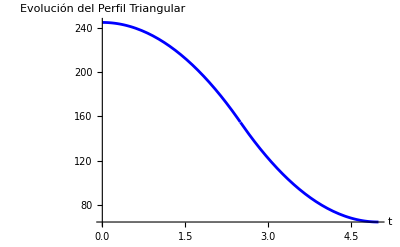

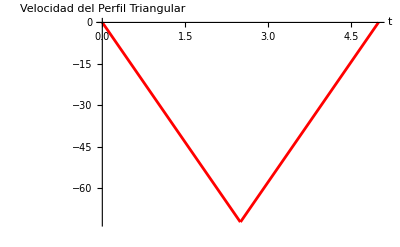

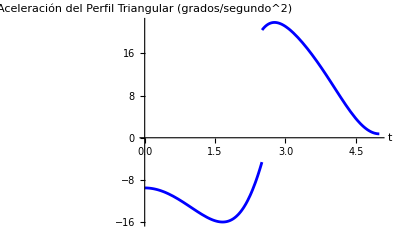

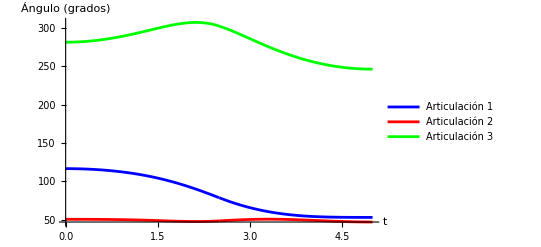

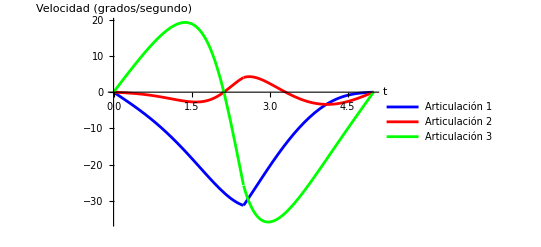

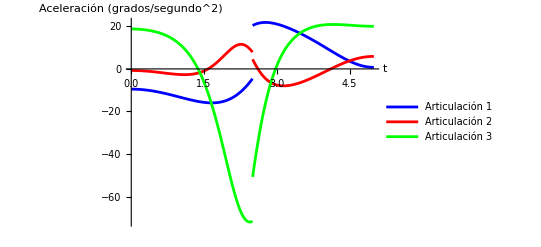

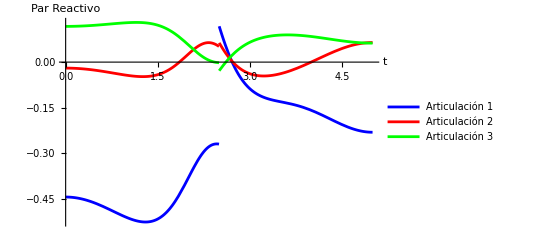

```mathematica
(*Suposición:los eslabones están hecho de MDF*)(*densidad MDF=500[kg/m^3]*)(*densidad ABS=1040[kg/m^3]*)(*Se considerará un peso 10 veces menor,pues los eslaboness serán diseñados para tener el material minimo en manufactura aditiva*)ρ=1040/10;
g=-9.81;(*Aceleración gravitatoria*)

(*Datos del eslabón 1 o Cilindro*)
d1=15;(*Valor de d1/Altura del cilindro*)
RadCil=2.5;(*Radio Cilindro*)
m[1]=ρ (π (RadCil/100)^2*(d1/100));(*masa del cilindro*)

(*Datos del eslabón 2*)
e2=5;(*Espesor eslabón 2*)
g2=5;(*Ancho eslabón 2*)
l2=25;(*Largo eslabón 2*)
m[2]=ρ (e2/100) (g2/100) (l2/100);(*masa eslabón 2*)

(*Datos del eslabón 3*)
e3=5;(*Espesor eslabón 3*)
g3=5;(*Ancho eslabón 3*)
l3=20;(*Largo eslabón 3*)
m[3]=ρ (e3/100) (g3/100) (l3/100);(*masa eslabón 3*)


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Construcción del plano de trabajo*)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(*Calcular vectores en el plano*)
vectorAB=NB-NA;
vectorAD=ND-NA;

(*Calcular el centro y el radio del semiarco*)
Centro=(NA+NC)/2; (*Centro entre NA y NC*)
Radio=Norm[NA-NC]/2;  (*Radio es la mitad de la distancia entre NA y NC*)

(*ARCO DE NA A NC POR ARRIBA*)
ANGPARTIDA=245; (*Ángulo de partida en grados*)
ANGFINAL=64.5; (*Ángulo final en grados*)

tf=5; (*Tiempo de operación*)
qf=ANGFINAL-ANGPARTIDA; (*Cambio total de ángulo*)

(*Perfil de trayectoria triangular para theta*)
theta=Piecewise[{{(2*qf/tf^2)*t^2,t<tf/2},{(-2*qf/tf^2)*t^2+(4*qf/tf)*t-qf,t>=tf/2}}]+ANGPARTIDA;

(*Parametrizando la semicircunferencia en un plano paralelo*)
x=Centro[[1]]+Radio*Cos[theta*Degree]*vectorAB[[1]]/Norm[vectorAB]+Radio*Sin[theta*Degree]*vectorAD[[1]]/Norm[vectorAD];
y=Centro[[2]]+Radio*Cos[theta*Degree]*vectorAB[[2]]/Norm[vectorAB]+Radio*Sin[theta*Degree]*vectorAD[[2]]/Norm[vectorAD];
z=Centro[[3]]+Radio*Cos[theta*Degree]*vectorAB[[3]]/Norm[vectorAB]+Radio*Sin[theta*Degree]*vectorAD[[3]]/Norm[vectorAD];

(*Generar puntos de la semicircunferencia*)
puntosSemicirc=Table[{x,y,z}/. t->tiempo,{tiempo,0,tf,tf/50}];

(*Línea de la semicircunferencia con etiquetas de punto inicial y final*)
lineaSemicirc=Line[puntosSemicirc];

(*Añadir etiquetas de punto inicial (NA),final (NC),y punto de inicio de la semicircunferencia*)
etiquetas={Text["NA",NA,{2,0}],Text["NB",NB,{2,0}],Text["NC",NC,{-2,0}],Text["ND",ND,{-2,0}]};

(*Gráfico 3D con las etiquetas y la semicircunferencia*)
Graphics3D[{{plano,Red,lineaSemicirc},etiquetas},Boxed->False]

(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Longitud eslabón 1*)
l1=d1;

(*l2 y l3 conocidos desde el inicio*)
(*l4,l5,l6,α,β t γ vienen del análisis de la cinemática inversa*)

l4=z-l1;
l5=Sqrt[x^2+y^2];
l6=Sqrt[l4^2+l5^2];

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,Sqrt[4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2]];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,Sqrt[4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2]];
θ[3]=γ+π;

(*Derivadas articulares*)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];

(******************)

(*Modelado Directo*)
T01=({{Cos[θ[1]],0,Sin[θ[1]],0},{Sin[θ[1]],0,-Cos[θ[1]],0},{0,1,0,d1},{0,0,0,1}});
T12=({{Cos[θ[2]],-Sin[θ[2]],0,l2 Cos[θ[2]]},{Sin[θ[2]],Cos[θ[2]],0,l2 Sin[θ[2]]},{0,0,1,0},{0,0,0,1}});
T23=({{Cos[θ[3]],-Sin[θ[3]],0,l3 Cos[θ[3]]},{Sin[θ[3]],Cos[θ[3]],0,l3 Sin[θ[3]]},{0,0,1,0},{0,0,0,1}});
H=({{1,0,0,0},{0,1,0,0},{0,0,1,0}});

(*Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(*Construcción eslabón 1*)
(*Separación del centro de la base respecto al marco de trabajo*)
Sep=0;
(*Centro de la base*)
CenBase={0,Sep,0};
(*Centro de la tapa*)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];
(*Construcción eslabón 2*)
(*Puntos en coordenadas homogéneas*)
V1={0,1/2 g2,1/2 e2,1};
V2={0,-(1/2) g2,1/2 e2,1};
V3={0,-(1/2) g2,-(1/2) e2,1};
V4={0,1/2 g2,-(1/2) e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-(1/2) g2,1/2 e2,1};
V7={-l2,-(1/2) g2,-(1/2) e2,1};
V8={-l2,1/2 g2,-(1/2) e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};

(*Construcción eslabón 3*)
N1={0,1/2 g3,1/2 e3,1};
N2={0,-(1/2) g3,1/2 e3,1};
N3={0,-(1/2) g3,-(1/2) e3,1};
N4={0,1/2 g3,-(1/2) e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-(1/2) g3,1/2 e3,1};
N7={-l3,-(1/2) g3,-(1/2) e3,1};
N8={-l3,1/2 g3,-(1/2) e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};

imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Black,lineaSemicirc},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(*Gráficas de los pares reactivos*)
τm1=1.5/100 (1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100 (1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100 (1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));



(*Gráfica de la evolución del perfil Triangular*)
Plot[theta,{t,0,tf},AxesLabel->{"t","Evolución del Perfil Triangular"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la velocidad del perfil Triangular*)
velocidadPerfil=D[theta,t];

(*Gráfica de la velocidad del perfil Triangular*)
Plot[velocidadPerfil,{t,0,tf},AxesLabel->{"t","Velocidad del Perfil Triangular"},PlotStyle->Red,AxesStyle->Directive[Thick,Black]]

(*Gráfica de Aceleración del Perfil Triangular*)
Plot[θpp[1] (180/π),{t,0,tf},AxesLabel->{"t","Aceleración del Perfil Triangular (grados/segundo^2)"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Gráfica del desplazamiento articular de cada articulación*)
Plot[{θ[1] (180/π),θ[2] (180/π),θ[3] (180/π)},{t,0,tf},AxesLabel->{"t","Ángulo (grados)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (velocidad) de cada articulación*)
Plot[{θp[1] (180/π),θp[2] (180/π),θp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Velocidad (grados/segundo)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (aceleración) de cada articulación*)
Plot[{θpp[1] (180/π),θpp[2] (180/π),θpp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Aceleración (grados/segundo^2)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de los pares reactivos*)
Plot[{τm1,τm2,τm3},{t,0,tf},AxesLabel->{"t","Par Reactivo"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]
```

SEMIARCO 1A2 QUINTICO

-Graphics3D-

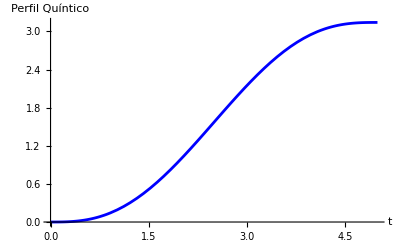

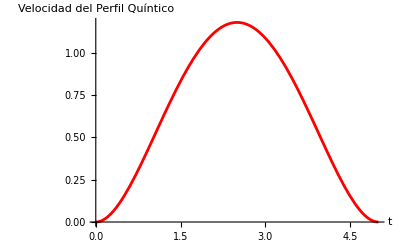

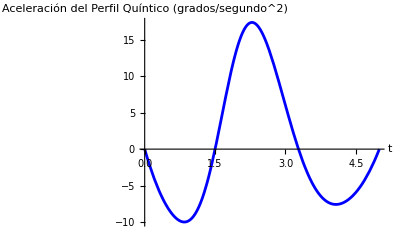

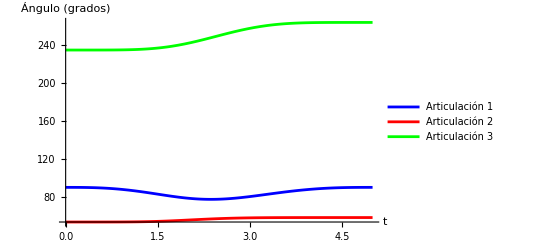

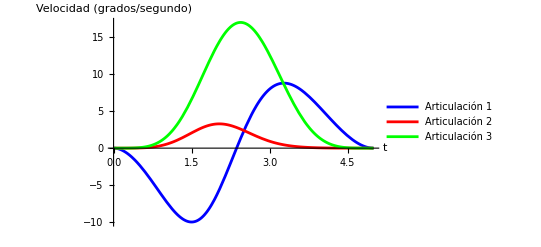

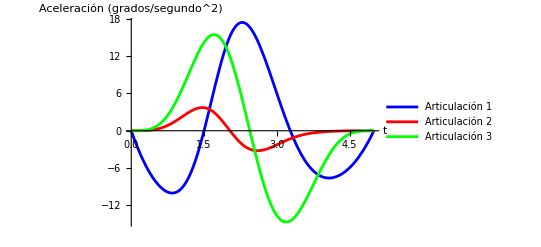

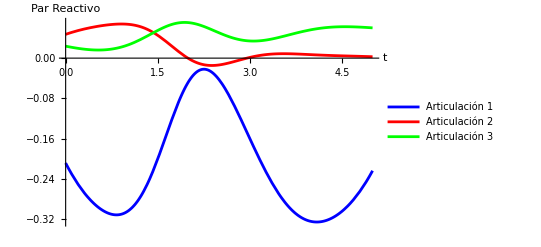

```mathematica
SEMIARCO 1A2 QUINTICO
(*Suposición:los eslabones están hecho de MDF*)(*densidad MDF=500[kg/m^3]*)(*densidad ABS=1040[kg/m^3]*)(*Se considerará un peso 10 veces menor,pues los eslaboness serán diseñados para tener el material minimo en manufactura aditiva*)ρ=1040/10;
g=-9.81;(*Aceleración gravitatoria*)

(*Datos del eslabón 1 o Cilindro*)
d1=15;(*Valor de d1/Altura del cilindro*)
RadCil=2.5;(*Radio Cilindro*)
m[1]=ρ (π (RadCil/100)^2*(d1/100));(*masa del cilindro*)

(*Datos del eslabón 2*)
e2=5;(*Espesor eslabón 2*)
g2=5;(*Ancho eslabón 2*)
l2=25;(*Largo eslabón 2*)
m[2]=ρ (e2/100) (g2/100) (l2/100);(*masa eslabón 2*)

(*Datos del eslabón 3*)
e3=5;(*Espesor eslabón 3*)
g3=5;(*Ancho eslabón 3*)
l3=20;(*Largo eslabón 3*)
m[3]=ρ (e3/100) (g3/100) (l3/100);(*masa eslabón 3*)


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Construcción del plano de trabajo*)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(*Calcular vectores en el plano*)vectorAB=NB-NA;
vectorAD=ND-NA;

(*Calcular el centro y el radio del semiarco*)
Centro=(NA+NC)/2;
Radio=Norm[NA-NC]/6;  (*Reducir el radio a un tercio de la distancia original*)

(*Perfil de trayectoria quíntico*)
tf=5; (*Tiempo de operación*)
theta=Pi (10 (t/tf)^3-15 (t/tf)^4+6 (t/tf)^5);

(*Parametrizando el semiarco en el plano correcto*)
x=Centro[[1]]+Radio*Cos[theta]*vectorAB[[1]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[1]]/Norm[vectorAD];
y=Centro[[2]]+Radio*Cos[theta]*vectorAB[[2]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[2]]/Norm[vectorAD];
z=Centro[[3]]+Radio*Cos[theta]*vectorAB[[3]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[3]]/Norm[vectorAD];

(*Generar puntos de la semicircunferencia*)
puntosSemicirc=Table[{Centro[[1]]+Radio*Cos[theta]*vectorAB[[1]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[1]]/Norm[vectorAD],Centro[[2]]+Radio*Cos[theta]*vectorAB[[2]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[2]]/Norm[vectorAD],Centro[[3]]+Radio*Cos[theta]*vectorAB[[3]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[3]]/Norm[vectorAD]},{theta,0,Pi,Pi/50}];
(*Línea de la semicircunferencia*)
lineaSemicirc=Line[puntosSemicirc];

(*Añadir etiquetas*)
etiquetas={Text["NA",NA,{2,0}],Text["NB",NB,{2,0}],Text["NC",NC,{-2,0}],Text["ND",ND,{-2,0}]};

Graphics3D[{plano,Red,lineaSemicirc,etiquetas}]

(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Longitud eslabón 1*)
l1=d1;

(*l2 y l3 conocidos desde el inicio*)
(*l4,l5,l6,α,β t γ vienen del análisis de la cinemática inversa*)

l4=z-l1;
l5=Sqrt[x^2+y^2];
l6=Sqrt[l4^2+l5^2];

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,Sqrt[4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2]];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,Sqrt[4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2]];
θ[3]=γ+π;

(*Derivadas articulares*)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];

(******************)

(*Modelado Directo*)
T01=({{Cos[θ[1]],0,Sin[θ[1]],0},{Sin[θ[1]],0,-Cos[θ[1]],0},{0,1,0,d1},{0,0,0,1}});
T12=({{Cos[θ[2]],-Sin[θ[2]],0,l2 Cos[θ[2]]},{Sin[θ[2]],Cos[θ[2]],0,l2 Sin[θ[2]]},{0,0,1,0},{0,0,0,1}});
T23=({{Cos[θ[3]],-Sin[θ[3]],0,l3 Cos[θ[3]]},{Sin[θ[3]],Cos[θ[3]],0,l3 Sin[θ[3]]},{0,0,1,0},{0,0,0,1}});
H=({{1,0,0,0},{0,1,0,0},{0,0,1,0}});

(*Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(*Construcción eslabón 1*)
(*Separación del centro de la base respecto al marco de trabajo*)
Sep=0;
(*Centro de la base*)
CenBase={0,Sep,0};
(*Centro de la tapa*)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];
(*Construcción eslabón 2*)
(*Puntos en coordenadas homogéneas*)
V1={0,1/2 g2,1/2 e2,1};
V2={0,-(1/2) g2,1/2 e2,1};
V3={0,-(1/2) g2,-(1/2) e2,1};
V4={0,1/2 g2,-(1/2) e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-(1/2) g2,1/2 e2,1};
V7={-l2,-(1/2) g2,-(1/2) e2,1};
V8={-l2,1/2 g2,-(1/2) e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};

(*Construcción eslabón 3*)
N1={0,1/2 g3,1/2 e3,1};
N2={0,-(1/2) g3,1/2 e3,1};
N3={0,-(1/2) g3,-(1/2) e3,1};
N4={0,1/2 g3,-(1/2) e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-(1/2) g3,1/2 e3,1};
N7={-l3,-(1/2) g3,-(1/2) e3,1};
N8={-l3,1/2 g3,-(1/2) e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};

imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Black,lineaSemicirc},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(*Gráficas de los pares reactivos*)
τm1=1.5/100 (1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100 (1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100 (1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));



(*Gráfica de la evolución del perfil quíntico*)
Plot[theta,{t,0,tf},AxesLabel->{"t","Perfil Quíntico"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la velocidad del perfil quíntico*)
velocidadPerfil=D[theta,t];

(*Gráfica de la velocidad del perfil quíntico*)
Plot[velocidadPerfil,{t,0,tf},AxesLabel->{"t","Velocidad del Perfil Quíntico"},PlotStyle->Red,AxesStyle->Directive[Thick,Black]]

(*Gráfica de Aceleración del Perfil Quíntico*)
Plot[θpp[1] (180/π),{t,0,tf},AxesLabel->{"t","Aceleración del Perfil Quíntico (grados/segundo^2)"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Gráfica del desplazamiento articular de cada articulación*)
Plot[{θ[1] (180/π),θ[2] (180/π),θ[3] (180/π)},{t,0,tf},AxesLabel->{"t","Ángulo (grados)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (velocidad) de cada articulación*)
Plot[{θp[1] (180/π),θp[2] (180/π),θp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Velocidad (grados/segundo)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (aceleración) de cada articulación*)
Plot[{θpp[1] (180/π),θpp[2] (180/π),θpp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Aceleración (grados/segundo^2)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de los pares reactivos*)
Plot[{τm1,τm2,τm3},{t,0,tf},AxesLabel->{"t","Par Reactivo"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]
```

SEMIARCO 1A2 triangular

-Graphics3D-

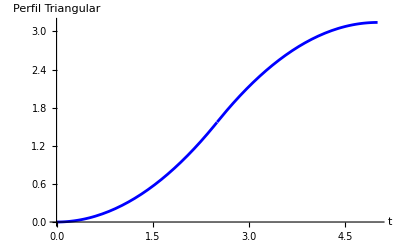

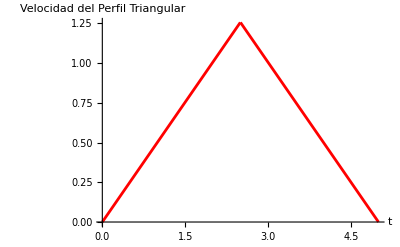

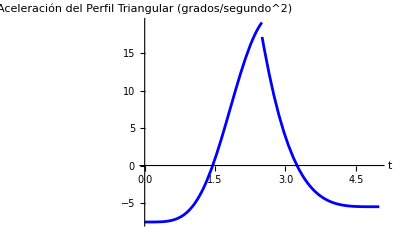

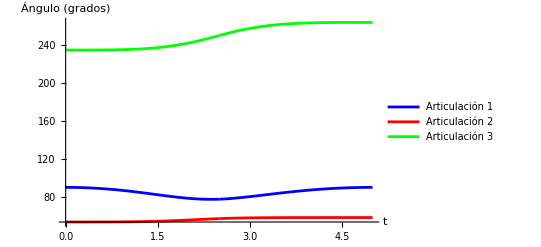

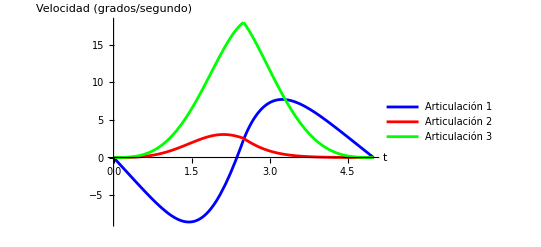

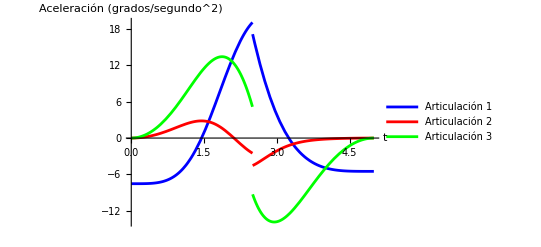

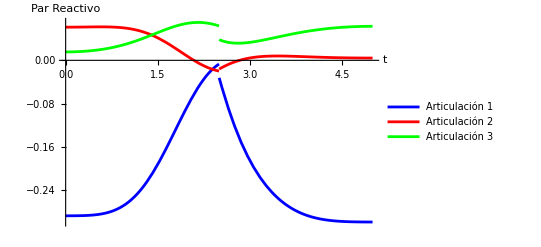

```mathematica
SEMIARCO 1A2 triangular

(*Suposición:los eslabones están hecho de MDF*)(*densidad MDF=500[kg/m^3]*)(*densidad ABS=1040[kg/m^3]*)(*Se considerará un peso 10 veces menor,pues los eslaboness serán diseñados para tener el material minimo en manufactura aditiva*)ρ=1040/10;
g=-9.81;(*Aceleración gravitatoria*)

(*Datos del eslabón 1 o Cilindro*)
d1=15;(*Valor de d1/Altura del cilindro*)
RadCil=2.5;(*Radio Cilindro*)
m[1]=ρ (π (RadCil/100)^2*(d1/100));(*masa del cilindro*)

(*Datos del eslabón 2*)
e2=5;(*Espesor eslabón 2*)
g2=5;(*Ancho eslabón 2*)
l2=25;(*Largo eslabón 2*)
m[2]=ρ (e2/100) (g2/100) (l2/100);(*masa eslabón 2*)

(*Datos del eslabón 3*)
e3=5;(*Espesor eslabón 3*)
g3=5;(*Ancho eslabón 3*)
l3=20;(*Largo eslabón 3*)
m[3]=ρ (e3/100) (g3/100) (l3/100);(*masa eslabón 3*)


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Construcción del plano de trabajo*)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(*Calcular vectores en el plano*)
vectorAB=NB-NA;
vectorAD=ND-NA;

(*Calcular el centro y el radio del semiarco*)
Centro=(NA+NC)/2;
Radio=Norm[NA-NC]/6;  (*Radio reducido a un tercio*)

(*Perfil de trayectoria triangular*)
tf=5;  (*Tiempo de operación*)
qf=Pi;  (*Cambio total de ángulo*)

(*Ecuación de theta para perfil triangular*)
theta=Piecewise[{{(2*qf/tf^2)*t^2,t<tf/2},{(-2*qf/tf^2)*t^2+(4*qf/tf)*t-qf,t>=tf/2}}];

(*Parametrizando el semiarco en el plano correcto*)
x=Centro[[1]]+Radio*Cos[theta]*vectorAB[[1]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[1]]/Norm[vectorAD];
y=Centro[[2]]+Radio*Cos[theta]*vectorAB[[2]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[2]]/Norm[vectorAD];
z=Centro[[3]]+Radio*Cos[theta]*vectorAB[[3]]/Norm[vectorAB]+Radio*Sin[theta]*vectorAD[[3]]/Norm[vectorAD];

(*Generar puntos de la semicircunferencia*)
puntosSemicirc=Table[{x,y,z},{t,0,tf,tf/50}];

(*Línea de la semicircunferencia*)
lineaSemicirc=Line[puntosSemicirc];

(*Añadir etiquetas*)
etiquetas={Text["NA",NA,{2,0}],Text["NB",NB,{2,0}],Text["NC",NC,{-2,0}],Text["ND",ND,{-2,0}]};

Graphics3D[{plano,Red,lineaSemicirc,etiquetas}]


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Longitud eslabón 1*)
l1=d1;

(*l2 y l3 conocidos desde el inicio*)
(*l4,l5,l6,α,β t γ vienen del análisis de la cinemática inversa*)

l4=z-l1;
l5=Sqrt[x^2+y^2];
l6=Sqrt[l4^2+l5^2];

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,Sqrt[4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2]];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,Sqrt[4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2]];
θ[3]=γ+π;

(*Derivadas articulares*)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];

(******************)

(*Modelado Directo*)
T01=({{Cos[θ[1]],0,Sin[θ[1]],0},{Sin[θ[1]],0,-Cos[θ[1]],0},{0,1,0,d1},{0,0,0,1}});
T12=({{Cos[θ[2]],-Sin[θ[2]],0,l2 Cos[θ[2]]},{Sin[θ[2]],Cos[θ[2]],0,l2 Sin[θ[2]]},{0,0,1,0},{0,0,0,1}});
T23=({{Cos[θ[3]],-Sin[θ[3]],0,l3 Cos[θ[3]]},{Sin[θ[3]],Cos[θ[3]],0,l3 Sin[θ[3]]},{0,0,1,0},{0,0,0,1}});
H=({{1,0,0,0},{0,1,0,0},{0,0,1,0}});

(*Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(*Construcción eslabón 1*)
(*Separación del centro de la base respecto al marco de trabajo*)
Sep=0;
(*Centro de la base*)
CenBase={0,Sep,0};
(*Centro de la tapa*)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];
(*Construcción eslabón 2*)
(*Puntos en coordenadas homogéneas*)
V1={0,1/2 g2,1/2 e2,1};
V2={0,-(1/2) g2,1/2 e2,1};
V3={0,-(1/2) g2,-(1/2) e2,1};
V4={0,1/2 g2,-(1/2) e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-(1/2) g2,1/2 e2,1};
V7={-l2,-(1/2) g2,-(1/2) e2,1};
V8={-l2,1/2 g2,-(1/2) e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};

(*Construcción eslabón 3*)
N1={0,1/2 g3,1/2 e3,1};
N2={0,-(1/2) g3,1/2 e3,1};
N3={0,-(1/2) g3,-(1/2) e3,1};
N4={0,1/2 g3,-(1/2) e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-(1/2) g3,1/2 e3,1};
N7={-l3,-(1/2) g3,-(1/2) e3,1};
N8={-l3,1/2 g3,-(1/2) e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};

imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Black,lineaSemicirc},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(*Gráficas de los pares reactivos*)
τm1=1.5/100 (1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100 (1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100 (1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));



(*Gráfica de la evolución del perfil triangular*)
Plot[theta,{t,0,tf},AxesLabel->{"t","Perfil Triangular"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la velocidad del perfil triangular*)
velocidadPerfil=D[theta,t];

(*Gráfica de la velocidad del perfil triangular*)
Plot[velocidadPerfil,{t,0,tf},AxesLabel->{"t","Velocidad del Perfil Triangular"},PlotStyle->Red,AxesStyle->Directive[Thick,Black]]

(*Gráfica de Aceleración del Perfil Triangular*)
Plot[θpp[1] (180/π),{t,0,tf},AxesLabel->{"t","Aceleración del Perfil Triangular (grados/segundo^2)"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Gráfica del desplazamiento articular de cada articulación*)
Plot[{θ[1] (180/π),θ[2] (180/π),θ[3] (180/π)},{t,0,tf},AxesLabel->{"t","Ángulo (grados)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (velocidad) de cada articulación*)
Plot[{θp[1] (180/π),θp[2] (180/π),θp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Velocidad (grados/segundo)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (aceleración) de cada articulación*)
Plot[{θpp[1] (180/π),θpp[2] (180/π),θpp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Aceleración (grados/segundo^2)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de los pares reactivos*)
Plot[{τm1,τm2,τm3},{t,0,tf},AxesLabel->{"t","Par Reactivo"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]
```

```mathematica
RECTA QUINTICO
```

RECTA QUINTICO

-Graphics3D-

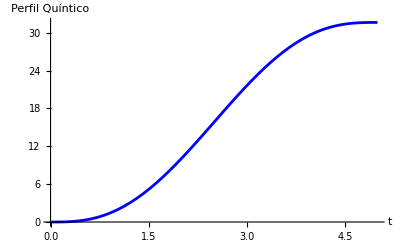

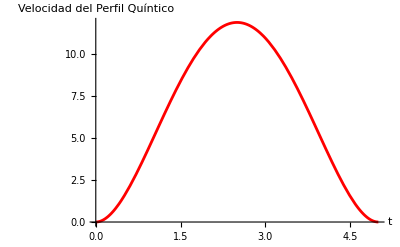

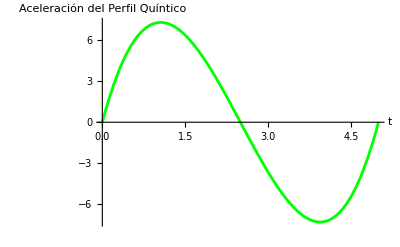

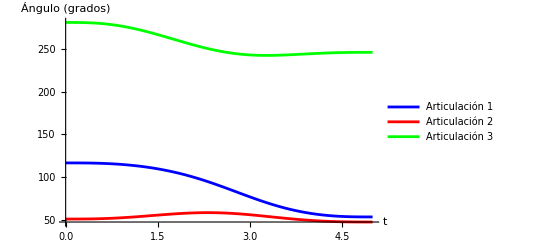

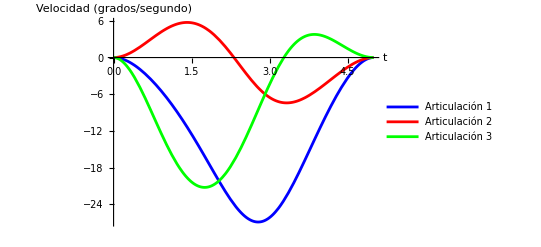

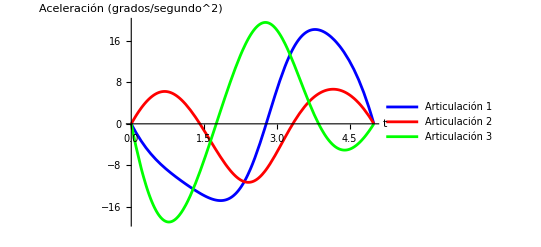

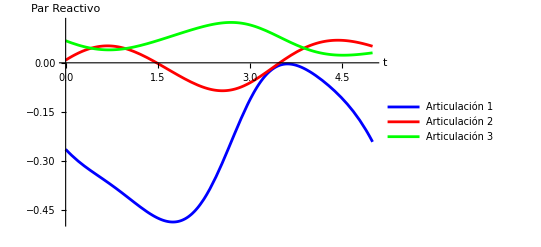

```mathematica
(*Suposición:los eslabones están hecho de MDF*)(*densidad MDF=500[kg/m^3]*)(*densidad ABS=1040[kg/m^3]*)(*Se considerará un peso 10 veces menor,pues los eslaboness serán diseñados para tener el material minimo en manufactura aditiva*)ρ=1040/10;
g=-9.81;(*Aceleración gravitatoria*)

(*Datos del eslabón 1 o Cilindro*)
d1=15;(*Valor de d1/Altura del cilindro*)
RadCil=2.5;(*Radio Cilindro*)
m[1]=ρ (π (RadCil/100)^2*(d1/100));(*masa del cilindro*)

(*Datos del eslabón 2*)
e2=5;(*Espesor eslabón 2*)
g2=5;(*Ancho eslabón 2*)
l2=25;(*Largo eslabón 2*)
m[2]=ρ (e2/100) (g2/100) (l2/100);(*masa eslabón 2*)

(*Datos del eslabón 3*)
e3=5;(*Espesor eslabón 3*)
g3=5;(*Ancho eslabón 3*)
l3=20;(*Largo eslabón 3*)
m[3]=ρ (e3/100) (g3/100) (l3/100);(*masa eslabón 3*)


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Construcción del plano de trabajo*)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(*Construcción de la trayectoria en línea recta*)
Linea=Line[{NA,NC}];
P0=NA;
Pf=NC;


(*Introducción del perfil quíntico*)
(*Longitud de la recta*)
qf=Sqrt[(Pf[[1]]-P0[[1]])^2+(Pf[[2]]-P0[[2]])^2]//N;
(*Tiempo de operación*)
tf=5;

(*Perfil de trayectoria quíntico*)
q=qf (10 (t/tf)^3-15 (t/tf)^4+6 (t/tf)^5);

(*Parametrizando la recta*)
x=P0[[1]]+q/qf (Pf[[1]]-P0[[1]]);
y=P0[[2]]+q/qf (Pf[[2]]-P0[[2]]);
z=P0[[3]]+q/qf (Pf[[3]]-P0[[3]]);

(*Añadir etiquetas*)
etiquetas={Text["NA",NA,{2,0}],Text["NB",NB,{2,0}],Text["NC",NC,{-2,0}],Text["ND",ND,{-2,0}]};

Graphics3D[{plano,Red,Linea,etiquetas}]

(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Longitud eslabón 1*)
l1=d1;

(*l2 y l3 conocidos desde el inicio*)
(*l4,l5,l6,α,β t γ vienen del análisis de la cinemática inversa*)

l4=z-l1;
l5=Sqrt[x^2+y^2];
l6=Sqrt[l4^2+l5^2];

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,Sqrt[4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2]];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,Sqrt[4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2]];
θ[3]=γ+π;

(*Derivadas articulares*)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];

(******************)

(*Modelado Directo*)
T01=({{Cos[θ[1]],0,Sin[θ[1]],0},{Sin[θ[1]],0,-Cos[θ[1]],0},{0,1,0,d1},{0,0,0,1}});
T12=({{Cos[θ[2]],-Sin[θ[2]],0,l2 Cos[θ[2]]},{Sin[θ[2]],Cos[θ[2]],0,l2 Sin[θ[2]]},{0,0,1,0},{0,0,0,1}});
T23=({{Cos[θ[3]],-Sin[θ[3]],0,l3 Cos[θ[3]]},{Sin[θ[3]],Cos[θ[3]],0,l3 Sin[θ[3]]},{0,0,1,0},{0,0,0,1}});
H=({{1,0,0,0},{0,1,0,0},{0,0,1,0}});

(*Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(*Construcción eslabón 1*)
(*Separación del centro de la base respecto al marco de trabajo*)
Sep=0;
(*Centro de la base*)
CenBase={0,Sep,0};
(*Centro de la tapa*)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];
(*Construcción eslabón 2*)
(*Puntos en coordenadas homogéneas*)
V1={0,1/2 g2,1/2 e2,1};
V2={0,-(1/2) g2,1/2 e2,1};
V3={0,-(1/2) g2,-(1/2) e2,1};
V4={0,1/2 g2,-(1/2) e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-(1/2) g2,1/2 e2,1};
V7={-l2,-(1/2) g2,-(1/2) e2,1};
V8={-l2,1/2 g2,-(1/2) e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};

(*Construcción eslabón 3*)
N1={0,1/2 g3,1/2 e3,1};
N2={0,-(1/2) g3,1/2 e3,1};
N3={0,-(1/2) g3,-(1/2) e3,1};
N4={0,1/2 g3,-(1/2) e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-(1/2) g3,1/2 e3,1};
N7={-l3,-(1/2) g3,-(1/2) e3,1};
N8={-l3,1/2 g3,-(1/2) e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};

imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Purple,Linea},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(*Gráficas de los pares reactivos*)
τm1=1.5/100 (1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100 (1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100 (1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));



(*Gráfica de la evolución del perfil quíntico*)
Plot[q,{t,0,tf},AxesLabel->{"t","Perfil Quíntico"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la velocidad del perfil quíntico*)
velocidadPerfil=D[q,t];

(*Gráfica de la velocidad del perfil quíntico*)
Plot[velocidadPerfil,{t,0,tf},AxesLabel->{"t","Velocidad del Perfil Quíntico"},PlotStyle->Red,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la aceleración del perfil quíntico*)
aceleracionPerfil=D[velocidadPerfil,t];

(*Gráfica de Aceleración del Perfil Quíntico*)
Plot[aceleracionPerfil,{t,0,tf},AxesLabel->{"t","Aceleración del Perfil Quíntico"},PlotStyle->Green,AxesStyle->Directive[Thick,Black]]


(*Gráfica del desplazamiento articular de cada articulación*)
Plot[{θ[1] (180/π),θ[2] (180/π),θ[3] (180/π)},{t,0,tf},AxesLabel->{"t","Ángulo (grados)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (velocidad) de cada articulación*)
Plot[{θp[1] (180/π),θp[2] (180/π),θp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Velocidad (grados/segundo)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (aceleración) de cada articulación*)
Plot[{θpp[1] (180/π),θpp[2] (180/π),θpp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Aceleración (grados/segundo^2)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de los pares reactivos*)
Plot[{τm1,τm2,τm3},{t,0,tf},AxesLabel->{"t","Par Reactivo"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]
```

RECTA TRIANGULAR

-Graphics3D-

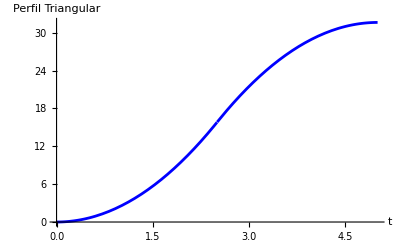

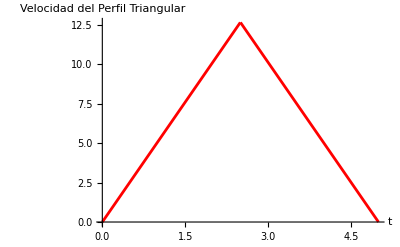

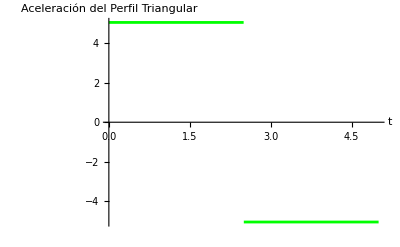

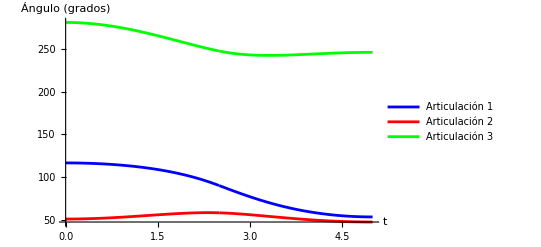

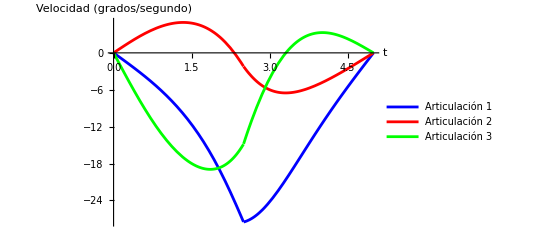

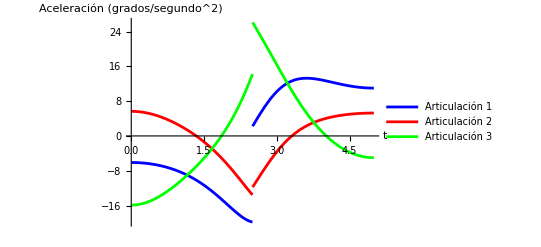

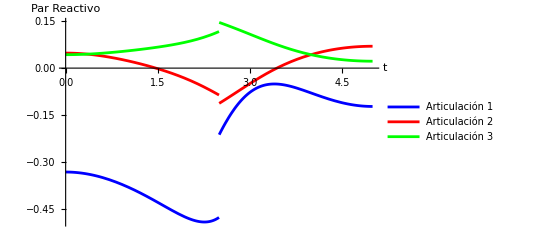

```mathematica
RECTA TRIANGULAR
(*Suposición:los eslabones están hecho de MDF*)(*densidad MDF=500[kg/m^3]*)(*densidad ABS=1040[kg/m^3]*)(*Se considerará un peso 10 veces menor,pues los eslaboness serán diseñados para tener el material minimo en manufactura aditiva*)ρ=1040/10;
g=-9.81;(*Aceleración gravitatoria*)

(*Datos del eslabón 1 o Cilindro*)
d1=15;(*Valor de d1/Altura del cilindro*)
RadCil=2.5;(*Radio Cilindro*)
m[1]=ρ (π (RadCil/100)^2*(d1/100));(*masa del cilindro*)

(*Datos del eslabón 2*)
e2=5;(*Espesor eslabón 2*)
g2=5;(*Ancho eslabón 2*)
l2=25;(*Largo eslabón 2*)
m[2]=ρ (e2/100) (g2/100) (l2/100);(*masa eslabón 2*)

(*Datos del eslabón 3*)
e3=5;(*Espesor eslabón 3*)
g3=5;(*Ancho eslabón 3*)
l3=20;(*Largo eslabón 3*)
m[3]=ρ (e3/100) (g3/100) (l3/100);(*masa eslabón 3*)


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Construcción del plano de trabajo*)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(*Construcción de la trayectoria en línea recta*)
Linea=Line[{NA,NC}];
P0=NA;
Pf=NC;

(*Longitud de la recta*)
qf=Sqrt[(Pf[[1]]-P0[[1]])^2+(Pf[[2]]-P0[[2]])^2]//N;
(*Tiempo de operación*)
tf=5;

(*Perfil de trayectoria triangular para q*)
q=Piecewise[{{(2*qf/tf^2)*t^2,t<tf/2},{(-2*qf/tf^2)*t^2+(4*qf/tf)*t-qf,t>=tf/2}}];

(*Parametrizando la recta*)
x=P0[[1]]+q/qf (Pf[[1]]-P0[[1]]);
y=P0[[2]]+q/qf (Pf[[2]]-P0[[2]]);
z=P0[[3]]+q/qf (Pf[[3]]-P0[[3]]);

(*Generar puntos de la línea recta*)
puntosLinea=Table[{x,y,z},{t,0,tf,tf/50}];

(*Línea de la trayectoria con etiquetas*)
lineaTrayectoria=Line[puntosLinea];

(*Añadir etiquetas*)
etiquetas={Text["NA",NA,{2,0}],Text["NB",NB,{2,0}],Text["NC",NC,{-2,0}],Text["ND",ND,{-2,0}]};

Graphics3D[{plano,Red,lineaTrayectoria,etiquetas}]


(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)
(*------------------------------------------------------------------------------------------------------------------*)

(*Longitud eslabón 1*)
l1=d1;

(*l2 y l3 conocidos desde el inicio*)
(*l4,l5,l6,α,β t γ vienen del análisis de la cinemática inversa*)

l4=z-l1;
l5=Sqrt[x^2+y^2];
l6=Sqrt[l4^2+l5^2];

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,Sqrt[4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2]];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,Sqrt[4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2]];
θ[3]=γ+π;

(*Derivadas articulares*)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];

(******************)

(*Modelado Directo*)
T01=({{Cos[θ[1]],0,Sin[θ[1]],0},{Sin[θ[1]],0,-Cos[θ[1]],0},{0,1,0,d1},{0,0,0,1}});
T12=({{Cos[θ[2]],-Sin[θ[2]],0,l2 Cos[θ[2]]},{Sin[θ[2]],Cos[θ[2]],0,l2 Sin[θ[2]]},{0,0,1,0},{0,0,0,1}});
T23=({{Cos[θ[3]],-Sin[θ[3]],0,l3 Cos[θ[3]]},{Sin[θ[3]],Cos[θ[3]],0,l3 Sin[θ[3]]},{0,0,1,0},{0,0,0,1}});
H=({{1,0,0,0},{0,1,0,0},{0,0,1,0}});

(*Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(*Construcción eslabón 1*)
(*Separación del centro de la base respecto al marco de trabajo*)
Sep=0;
(*Centro de la base*)
CenBase={0,Sep,0};
(*Centro de la tapa*)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];
(*Construcción eslabón 2*)
(*Puntos en coordenadas homogéneas*)
V1={0,1/2 g2,1/2 e2,1};
V2={0,-(1/2) g2,1/2 e2,1};
V3={0,-(1/2) g2,-(1/2) e2,1};
V4={0,1/2 g2,-(1/2) e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-(1/2) g2,1/2 e2,1};
V7={-l2,-(1/2) g2,-(1/2) e2,1};
V8={-l2,1/2 g2,-(1/2) e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};

(*Construcción eslabón 3*)
N1={0,1/2 g3,1/2 e3,1};
N2={0,-(1/2) g3,1/2 e3,1};
N3={0,-(1/2) g3,-(1/2) e3,1};
N4={0,1/2 g3,-(1/2) e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-(1/2) g3,1/2 e3,1};
N7={-l3,-(1/2) g3,-(1/2) e3,1};
N8={-l3,1/2 g3,-(1/2) e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};

imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Purple,Linea},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(*Gráficas de los pares reactivos*)
τm1=1.5/100 (1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100 (1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100 (1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));



(*Gráfica de la evolución del perfil Triangular*)
Plot[q,{t,0,tf},AxesLabel->{"t","Perfil Triangular"},PlotStyle->Blue,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la velocidad del perfil Triangular*)
velocidadPerfil=D[q,t];

(*Gráfica de la velocidad del perfil Triangular*)
Plot[velocidadPerfil,{t,0,tf},AxesLabel->{"t","Velocidad del Perfil Triangular"},PlotStyle->Red,AxesStyle->Directive[Thick,Black]]

(*Cálculo de la aceleración del perfil Triangular*)
aceleracionPerfil=D[velocidadPerfil,t];

(*Gráfica de Aceleración del Perfil Triangular*)
Plot[aceleracionPerfil,{t,0,tf},AxesLabel->{"t","Aceleración del Perfil Triangular"},PlotStyle->Green,AxesStyle->Directive[Thick,Black]]


(*Gráfica del desplazamiento articular de cada articulación*)
Plot[{θ[1] (180/π),θ[2] (180/π),θ[3] (180/π)},{t,0,tf},AxesLabel->{"t","Ángulo (grados)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (velocidad) de cada articulación*)
Plot[{θp[1] (180/π),θp[2] (180/π),θp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Velocidad (grados/segundo)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de las derivadas articulares (aceleración) de cada articulación*)
Plot[{θpp[1] (180/π),θpp[2] (180/π),θpp[3] (180/π)},{t,0,tf},AxesLabel->{"t","Aceleración (grados/segundo^2)"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]

(*Gráfica de los pares reactivos*)
Plot[{τm1,τm2,τm3},{t,0,tf},AxesLabel->{"t","Par Reactivo"},PlotLegends->{"Articulación 1","Articulación 2","Articulación 3"},PlotStyle->{Blue,Red,Green},AxesStyle->Directive[Thick,Black]]
```